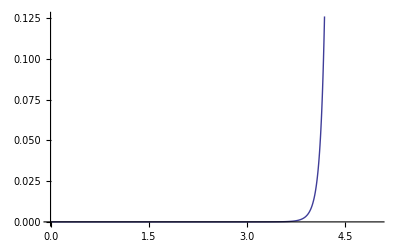

```mathematica
ϕ[r_]:=0.01(r-5)^-12

Plot[ϕ[r],{r,0,5}]
```

```mathematica
(-1+r)^12
```

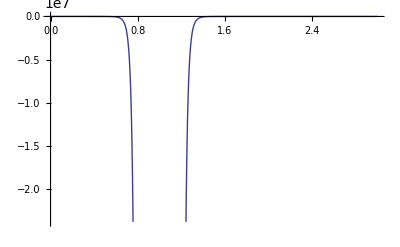

```mathematica
Plot[-1/(-1+r)^12,{r,0,3}]
```

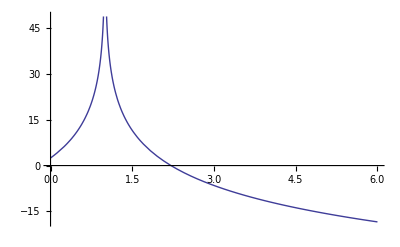

```mathematica
Plot[Log[Abs[-ϕ'[r]]],{r,0,6}]
```

```mathematica
d=1
τ=1
```

1

1

```mathematica
FindMaximum [Exp[-ϕ[r]/d -τ/(2 d) Abs[ϕ'[r]]^2 ]Abs[1+τ ϕ''[r]]Abs[1+τ ϕ'[r]/r],{r,3.1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{11.4872,{r→4.15497}}

FindMaximum::nrnum: The function value -ⅇ^0.000135947/d - 3.01739×10^-7\ τ/d\ Abs[1 - 0.004809\ τ]\ Abs[1 + 0.000250593\ τ] is not a real number at {r} = {3.1}.

```mathematica
FindMaximum[Exp[-ϕ[r]/d-(τ Abs[ϕ'[r]]^2)/(2 d)] Abs[1+τ ϕ''[r]] Abs[1+(τ ϕ'[r])/r],{r,3.5}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{11.4872,{r→4.15497}}

```mathematica
FindMaximum [Exp[-ϕ[x]/d -τ/(2 d) Abs[ϕ'[x]]^2 ]Abs[1+τ ϕ''[x]]Abs[r+τ ϕ'[x]],{x,2}]
```

FindMaximum::nrnum: The function value -1.\ Abs[7.52671×10^-8 + r] is not a real number at {x} = {2.}.

FindMaximum[Exp[-ϕ[x]/d-(τ Abs[ϕ'[x]]^2)/(2 d)] Abs[1+τ ϕ''[x]] Abs[r+τ ϕ'[x]],{x,2}]

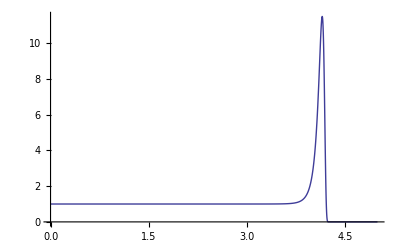

```mathematica
Plot[Exp[-ϕ[r]/d-(τ Abs[ϕ'[r]]^2)/(2 d)] Abs[1+τ ϕ''[r]] Abs[1+(τ ϕ'[r])/r],{r,0,5},PlotRange->All]
```

```mathematica
Plot[(-ϕ[x]/d -τ/(2 d) Abs[ϕ'[x]]^2 )+Log[Abs[1+τ ϕ''[x]]*Abs[x+τ ϕ'[x]]],{x,0,3}]
```

-Graphics-

ⅇ^(2039/8388608) Abs[3+τϕ'[3]] Abs[1+τϕ''[3]]